## Parallel Solow and Langevin

Solow growth:
dk/dt=s(k)f(k)-(δ+n)k
where we have the production function f(k)=Ax^α_1 and the savings rate s (k) = s_1+(s_2-s_1)/(1+ⅇ^(-s_3(k-d))) 
Solow growth can be written as
dx/dt=s(x)f(x)-(δ+n)x
dx/dt=s(x)f(x)-λx

Langevin dynamics:
dx/dt=-β dF/dx+σ dW/dt
where left term is deterministic, while right term is stochastic
F: energy landscape

### Simplified Solow model + Potential

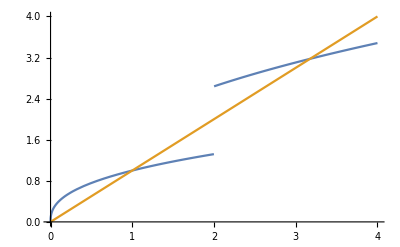

FindArgMin::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

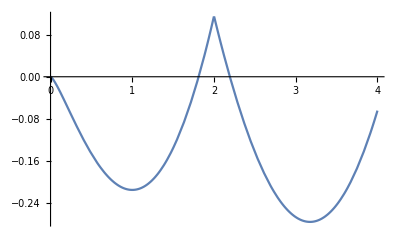

```mathematica
ClearAll[U,τ,δP];

A=10;α1=0.4;s1=0.1;s2=0.2;s3=10;d=2;n=0.5;

(* Solow growth *)
f[x_]:=A x^α1;
s[x_]:=If[x≤d,s1,s2]
(* s[x_]:=If[x≤0.5||0.6<x≤d,s1,s2] *)
δP[x_]:=If[x<1.95&&x>1.85,0.5,0.5];
Depreciation[x_]:=(δP[x]+n) x

Plot[{f[x] s[x],Depreciation[x]},{x,0,4}]

(* Potential based on Langevin dynamics *)
U[x_]=-(Integrate[f[x] s[x]-Depreciation[x],x]);
xmin1=#&@@FindArgMin[U[x],{x,1}];
xmin2=#&@@FindArgMin[U[x],{x,3}];
U2[x_?NumericQ]:=U[x/L];
Plot[Evaluate[U[x]],{x,0,4}]
```

#### Original Solow model + Potential

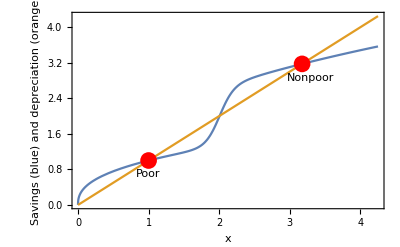

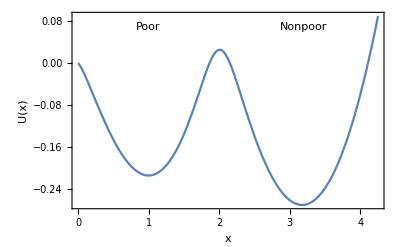

```mathematica
ClearAll[f,s,Depreciation,U,int,int2,sol,τ];

A=10;α1=0.4;s1=0.1;s2=0.2;s3=10;d=2;δP=0.5;n=0.5;

(* Solow growth *)

f[x_]:=A x^α1;
s[x_]:=s1+(s2-s1)/(1+Exp[-s3 (x-d)]); 
Depreciation[x_]:=(δP+n) x

data:={{1.00008,1.00008},{3.174781185869739,3.174781185869739}};
p1=Plot[{f[x] s[x],Depreciation[x]},{x,0,4.25}, 
Frame->True, FrameLabel->{"x", "Savings (blue) and depreciation (orange)"},LabelStyle->Medium];
p2=Graphics[{Red,PointSize[0.03],Point[data]}];
p3=Graphics[{Text[Poor,{1,0.7}],Text[Nonpoor,{3.3,2.85}]}];
Show[{p1,p2,p3}]


int=NDSolveValue[{U'[x]==-(f[x]s[x] -Depreciation[x]),U[0]==0},U,{x,0,4.25}];
p1=Plot[int[x],{x,0,4.25},Frame->True,FrameLabel->{"x","U(x)"},Axes->False,LabelStyle->Medium];
p2=Graphics[{Text[Poor,{1,0.07}],Text[Nonpoor,{3.2,0.07}]}];
Show[{p1,p2}]
```

## Changing parameters in Solow

#### Parameter A

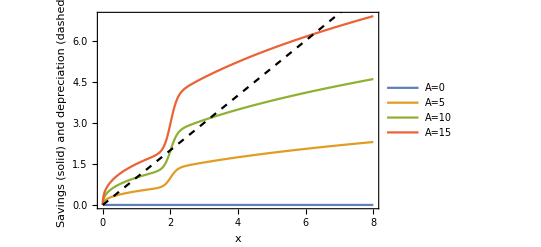

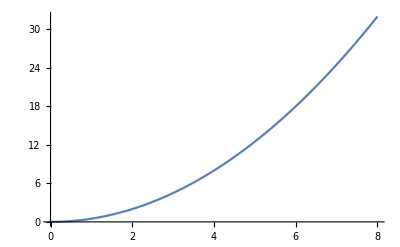
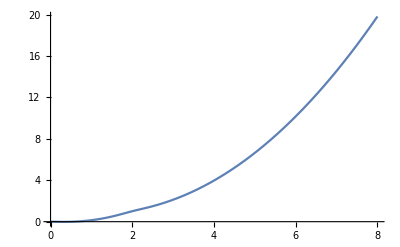
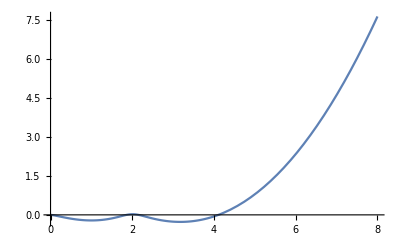
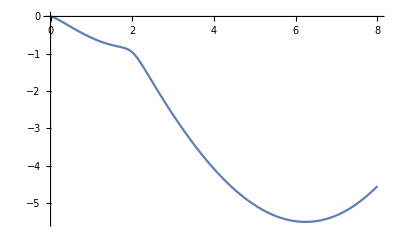

```mathematica
α1=0.4;s1=0.1;s2=0.2;s3=10;d=2;δP=0.5;n=0.5;

f[x_]:=A x^α1;
s[x_]:=s1+(s2-s1)/(1+Exp[-s3 (x-d)]); 
Depreciation[x_]:=(δP+n) x
Savings[x_]:=s[x] f[x]

ValuesA={0,5, 10,15};
p1=Plot[Evaluate[Table[Savings[x], {A, ValuesA}]], {x,0,8},
Frame->True, FrameLabel->{"x", "Savings (solid) and
 depreciation (dashed)"},
LabelStyle->Medium,PlotLegends->Placed[Table[Row[{"A=",x}],{x,ValuesA}],{Left,Top}]];
p2=Plot[Depreciation[x],{x,0,8},PlotStyle->{Black,Dashed}];
Show[{p1,p2}]

Evaluate[Table[int=NDSolveValue[{U'[x]==-(f[x]s[x] -Depreciation[x]),U[0]==0},U,{x,0,8}];
Plot[int[x],{x,0,8}],{A, ValuesA}]]
(* int:=NDSolveValue[{U'[x]==-(Savings[x] -Depreciation[x]),U[0]==0},U,{x,0,8}]
Plot[Evaluate@Table[int[x],{A,ValuesA}],{x,0,8},PlotRange->{-4,10}] *)
```

#### Parameter α1

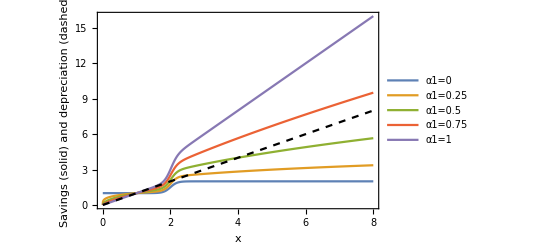

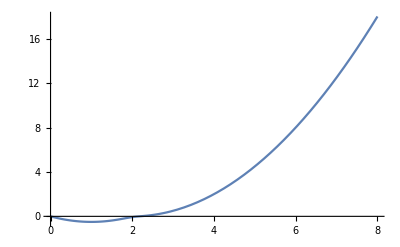
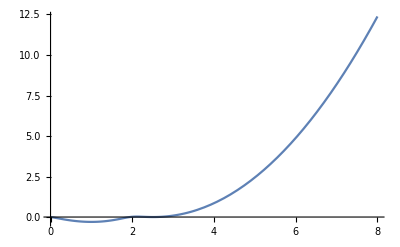
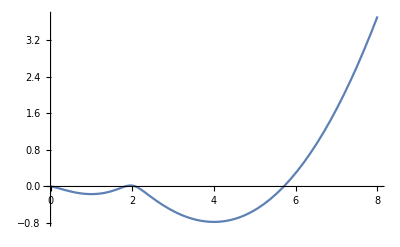
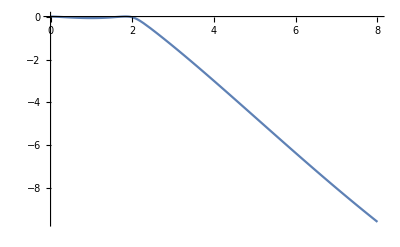
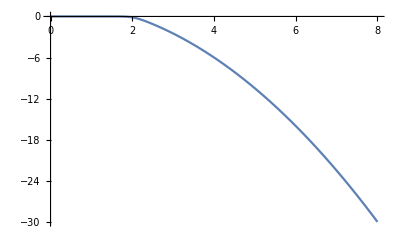

```mathematica
A=10;s1=0.1;s2=0.2;s3=10;d=2;δP=0.5;n=0.5;

f[x_]:=A x^α1;
s[x_]:=s1+(s2-s1)/(1+Exp[-s3 (x-d)]); 
Depreciation[x_]:=(δP+n) x
Savings[x_]:=s[x] f[x]

Valuesα1={0, 0.25,0.5,0.75,1};
p1=Plot[Evaluate[Table[Savings[x], {α1, Valuesα1}]], {x,0,8},
Frame->True, FrameLabel->{"x", "Savings (solid) and
 depreciation (dashed)"},
LabelStyle->Medium,PlotLegends->Placed[Table[Row[{"α1=",x}],{x,Valuesα1}],{Left,Top}]];
p2=Plot[Depreciation[x],{x,0,8},PlotStyle->{Black,Dashed}];
Show[{p1,p2}]

Evaluate[Table[int=NDSolveValue[{U'[x]==-(f[x]s[x] -Depreciation[x]),U[0]==0},U,{x,0,8}];
Plot[int[x],{x,0,8}],{α1, Valuesα1}]]
(* int:=NDSolveValue[{U'[x]==-(Savings[x] -Depreciation[x]),U[0]==0},U,{x,0,8}]
Plot[Evaluate@Table[int[x],{α1, Valuesα1}],{x,0,8},PlotRange->{-4,10}] *)
```

#### Parameter s1

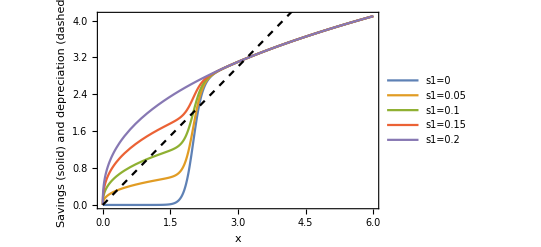

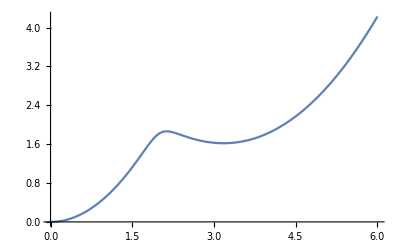
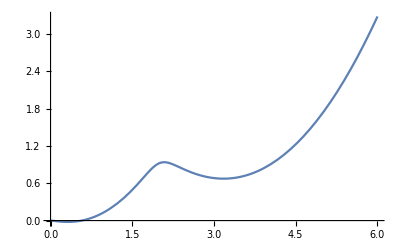
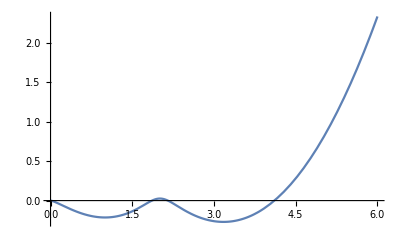
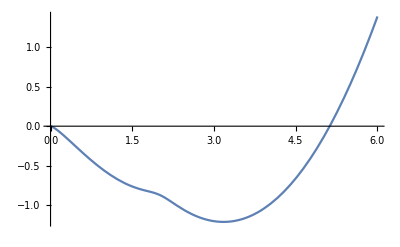
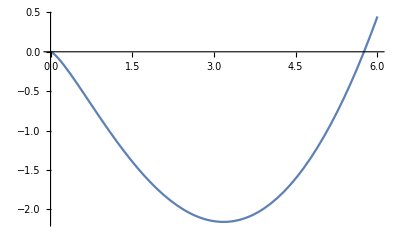

```mathematica
A=10;α1=0.4;s2=0.2;s3=10;d=2;δP=0.5;n=0.5;

f[x_]:=A x^α1;
s[x_]:=s1+(s2-s1)/(1+Exp[-s3 (x-d)]); 
Depreciation[x_]:=(δP+n) x
Savings[x_]:=s[x] f[x]

Valuess1={0,0.05,0.1,0.15,0.2};
p1=Plot[Evaluate[Table[Savings[x], {s1, Valuess1}]], {x,0,6},
Frame->True, FrameLabel->{"x", "Savings (solid) and
 depreciation (dashed)"},
LabelStyle->Medium,PlotLegends->Placed[Table[Row[{"s1=",x}],{x,Valuess1}],{Right,Bottom}]];
p2=Plot[Depreciation[x],{x,0,6},PlotStyle->{Black,Dashed}];
Show[{p1,p2}]

Evaluate[Table[int=NDSolveValue[{U'[x]==-(f[x]s[x] -Depreciation[x]),U[0]==0},U,{x,0,6}];
Plot[int[x],{x,0,6}],{s1, Valuess1}]]
(* int:=NDSolveValue[{U'[x]==-(Savings[x] -Depreciation[x]),U[0]==0},U,{x,0,8}]
Plot[Evaluate@Table[int[x],{s1, Valuess1}],{x,0,8},PlotRange->{-4,10}] *)
```

#### Parameter s2

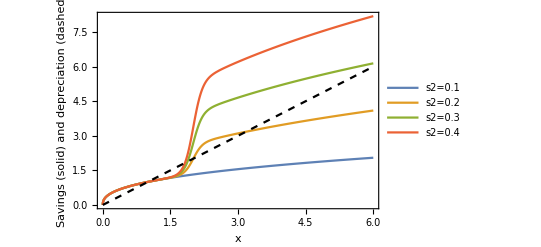

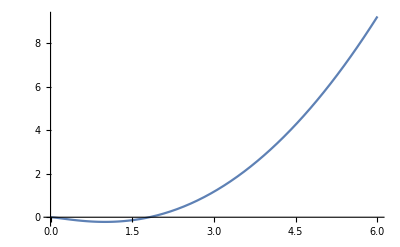
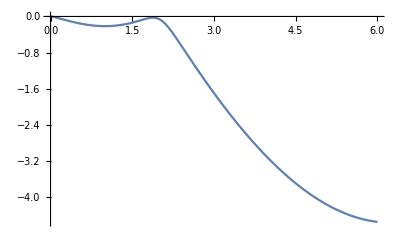
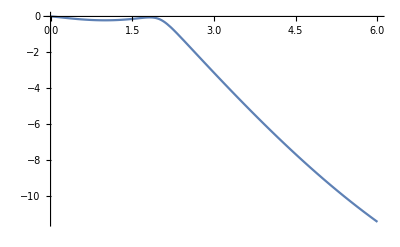
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
A=10;α1=0.4;s1=0.1;s3=10;d=2;δP=0.5;n=0.5;

f[x_]:=A x^α1;
s[x_]:=s1+(s2-s1)/(1+Exp[-s3 (x-d)]); 
Depreciation[x_]:=(δP+n) x
Savings[x_]:=s[x] f[x]

Valuess2={0.1,0.2,0.3,0.4};
p1=Plot[Evaluate[Table[Savings[x], {s2, Valuess2}]], {x,0,6},
Frame->True, FrameLabel->{"x", "Savings (solid) and
 depreciation (dashed)"},
LabelStyle->Medium,PlotLegends->Placed[Table[Row[{"s2=",x}],{x,Valuess2}],{Left,Top}]];
p2=Plot[Depreciation[x],{x,0,6},PlotStyle->{Black,Dashed}];
Show[{p1,p2}]

Evaluate[Table[int=NDSolveValue[{U'[x]==-(f[x]s[x] -Depreciation[x]),U[0]==0},U,{x,0,6}];
Plot[int[x],{x,0,6}],{s2, Valuess2}]]
(* int:=NDSolveValue[{U'[x]==-(Savings[x] -Depreciation[x]),U[0]==0},U,{x,0,8}]
Plot[Evaluate@Table[int[x],{s2, Valuess2}],{x,0,8},PlotRange->{-4,10}] *)
```

#### Parameter s3

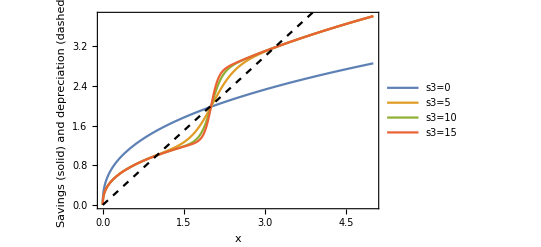

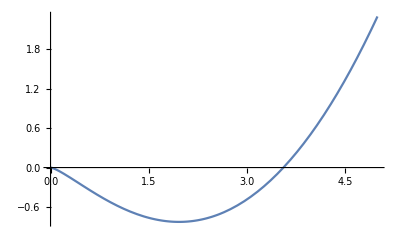
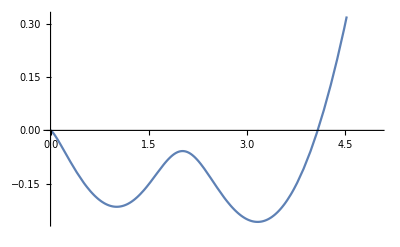
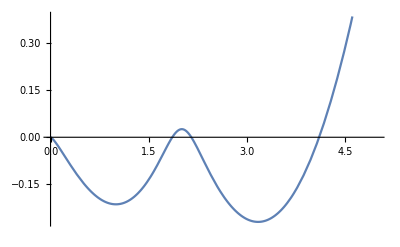
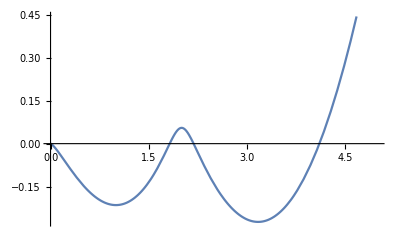

```mathematica
A=10;α1=0.4;s1=0.1;s2=0.2;d=2;δP=0.5;n=0.5;

f[x_]:=A x^α1;
s[x_]:=s1+(s2-s1)/(1+Exp[-s3 (x-d)]); 
Depreciation[x_]:=(δP+n) x
Savings[x_]:=s[x] f[x]

Valuess3={0,5, 10,15}; 
p1=Plot[Evaluate[Table[Savings[x], {s3, Valuess3}]], {x,0,5},
Frame->True, FrameLabel->{"x", "Savings (solid) and
 depreciation (dashed)"},
LabelStyle->Medium,PlotLegends->Placed[Table[Row[{"s3=",x}],{x,Valuess3}],{Right,Bottom}]];
p2=Plot[Depreciation[x],{x,0,5},PlotStyle->{Black,Dashed}];
Show[{p1,p2}]

Evaluate[Table[int=NDSolveValue[{U'[x]==-(f[x]s[x] -Depreciation[x]),U[0]==0},U,{x,0,5}];
Plot[int[x],{x,0,5}],{s3, Valuess3}]]
(* int:=NDSolveValue[{U'[x]==-(Savings[x] -Depreciation[x]),U[0]==0},U,{x,0,8}]
Plot[Evaluate@Table[int[x],{s3, Valuess3}],{x,0,8},PlotRange->{-4,10}] *)
```

#### Parameter d

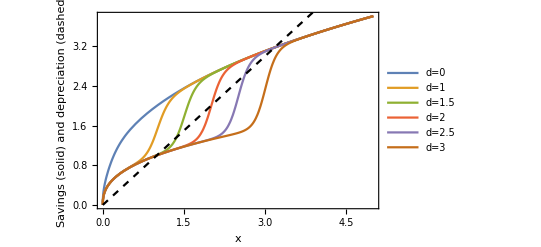

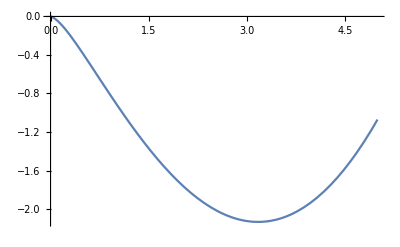
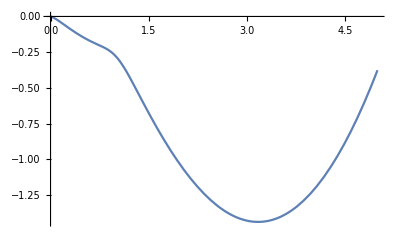
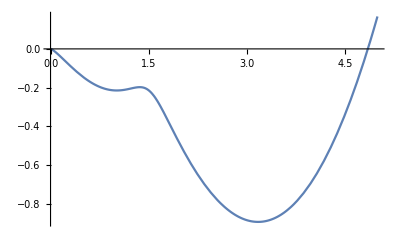
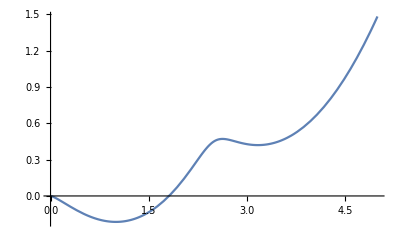
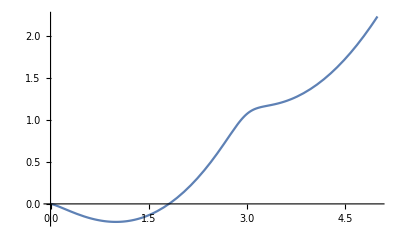
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
A=10;α1=0.4;s1=0.1;s2=0.2;s3=10;δP=0.5;n=0.5;

f[x_]:=A x^α1;
s[x_]:=s1+(s2-s1)/(1+Exp[-s3 (x-d)]); 
Depreciation[x_]:=(δP+n) x
Savings[x_]:=s[x] f[x]

Valuesd={0,1,1.5,2,2.5,3};
p1=Plot[Evaluate[Table[Savings[x], {d, Valuesd}]], {x,0,5},
Frame->True, FrameLabel->{"x", "Savings (solid) and
 depreciation (dashed)"},
LabelStyle->Medium,PlotLegends->Placed[Table[Row[{"d=",x}],{x,Valuesd}],{Right,Bottom}]];
p2=Plot[Depreciation[x],{x,0,5},PlotStyle->{Black,Dashed}];
Show[{p1,p2}]

Evaluate[Table[int=NDSolveValue[{U'[x]==-(f[x]s[x] -Depreciation[x]),U[0]==0},U,{x,0,5}];
Plot[int[x],{x,0,5}],{d, Valuesd}]]
(* int:=NDSolveValue[{U'[x]==-(Savings[x] -Depreciation[x]),U[0]==0},U,{x,0,8}]
Plot[Evaluate@Table[int[x],{d, Valuesd}],{x,0,8},PlotRange->{-4,10}] *)
```

#### Parameter δP or n

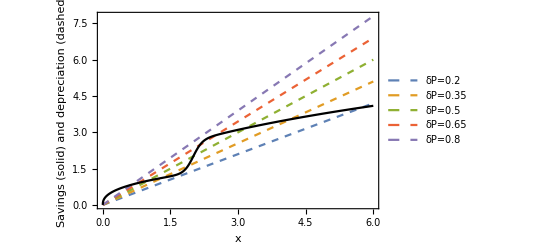

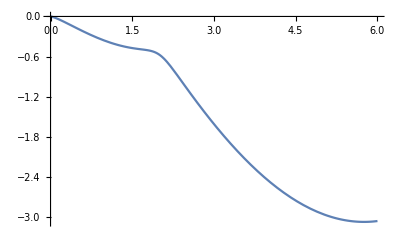
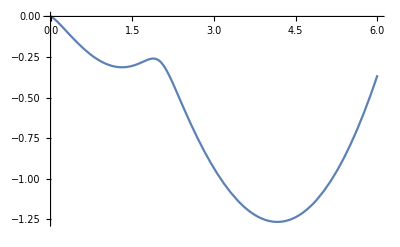
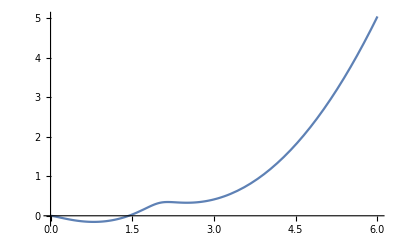
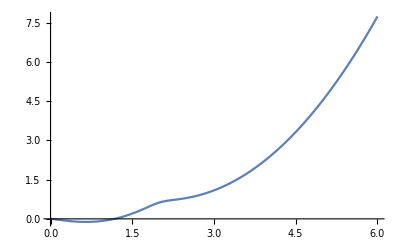
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
A=10;α1=0.4;s1=0.1;s2=0.2;s3=10;d=2;n=0.5;

f[x_]:=A x^α1;
s[x_]:=s1+(s2-s1)/(1+Exp[-s3 (x-d)]); 
Depreciation[x_]:=(δP+n) x
Savings[x_]:=s[x] f[x]

ValuesδP={0.2,0.35,0.5,0.65,0.8};
p1=Plot[Evaluate[Table[Depreciation[x], {δP, ValuesδP}]], {x,0,6},PlotStyle->Dashed,
Frame->True, FrameLabel->{"x", "Savings (solid) and
 depreciation (dashed)"},
LabelStyle->Medium,PlotLegends->Placed[Table[Row[{"δP=",x}],{x,ValuesδP}],{Left,Top}]];
p2=Plot[Savings[x],{x,0,6},PlotStyle->Black];
Show[{p1,p2}]

Evaluate[Table[int=NDSolveValue[{U'[x]==-(f[x]s[x] -Depreciation[x]),U[0]==0},U,{x,0,6}];
Plot[int[x],{x,0,6}],{δP, ValuesδP}]]
(* int:=NDSolveValue[{U'[x]==-(Savings[x] -Depreciation[x]),U[0]==0},U,{x,0,8}]
Plot[Evaluate@Table[int[x],{δP, ValuesδP}],{x,0,8},PlotRange->{-4,10}] *)
```

## Changing s(x) / δp(x)

### Changing depreciation function δp(x)

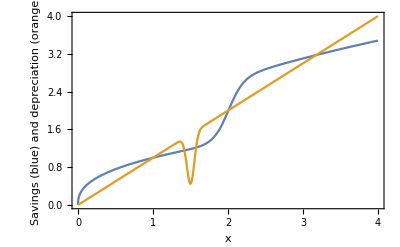

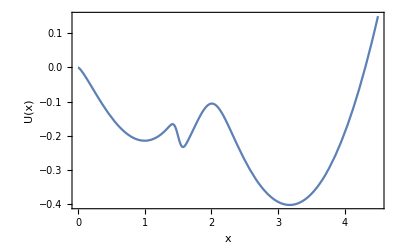

```mathematica
ClearAll[δP,f,s,Depreciation,U,int,int2,sol,τ];

A=10;α1=0.4;s1=0.1;s2=0.2;s3=10;d=2;n=0.5;
δ1=0.7;δ2=200;δ3=1.5;

f[x_]:=A x^α1;
s[x_]:=s1+(s2-s1)/(1+Exp[-s3 (x-d)]); 
(* δP[x_]:=If[x<1.8&&x>1.7,0,0.5]; *)
δP[x_]:=0.5-δ1 Exp[-δ2 (x-δ3)^2];
Depreciation[x_]:=(δP[x]+n) x;

(* min1=#&@@FindRoot[f[x]s[x]==Depreciation[x],{x,1}]
min2=#&@@FindRoot[f[x]s[x]==Depreciation[x],{x,2}]
min3=#&@@FindRoot[f[x]s[x]==Depreciation[x],{x,3}] *)

Plot[{f[x] s[x],Depreciation[x]},{x,0,4},Frame->True, FrameLabel->{"x", "Savings (blue) and
 depreciation (orange)"},LabelStyle->Medium]

int=NDSolveValue[{U'[x]==-(f[x]s[x] -Depreciation[x]),U[0]==0},U,{x,0,4.5}];
Plot[int[x],{x,0,4.5},Frame->True,FrameLabel->{"x","U(x)"},Axes->False,LabelStyle->Medium]
```

### Changing savings rate s(x)

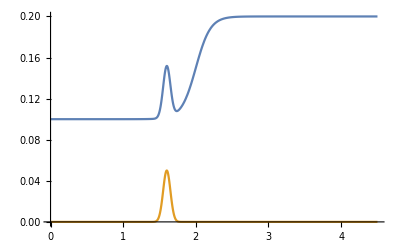

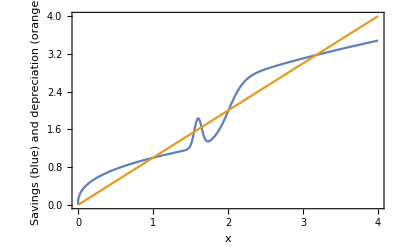

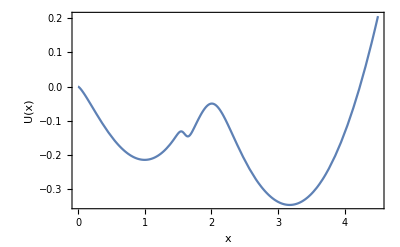

```mathematica
ClearAll[f,s,Depreciation,U,int,int2,sol,τ];

A=10;α1=0.4;s1=0.1;s2=0.2;s3=10;s4=0.05;s5=200;d1=2;d2=1.6;δP=0.5;n=0.5;

f[x_]:=A x^α1;
s[x_]:=s1+(s2-s1)/(1+Exp[-s3 (x-d1)])+s4 Exp[-s5 (x-d2)^2]; 
Depreciation[x_]:=(δP+n) x

(* min1=#&@@FindRoot[f[x]s[x]==Depreciation[x],{x,1}]
min2=#&@@FindRoot[f[x]s[x]==Depreciation[x],{x,2}]
min3=#&@@FindRoot[f[x]s[x]==Depreciation[x],{x,3}] *)

Plot[{s[x],s4 Exp[-s5 (x-d2)^2]},{x,0,4.5}]

Plot[{f[x] s[x],Depreciation[x]},{x,0,4},Frame->True, FrameLabel->{"x", "Savings (blue) and
 depreciation (orange)"}]

int=NDSolveValue[{U'[x]==-(f[x]s[x] -Depreciation[x]),U[0]==0},U,{x,0,4.5}];
Plot[int[x],{x,0,4.5},Frame->True,FrameLabel->{"x","U(x)"},Axes->False]

(*
int2[x_?NumericQ]:=int[x/L];
sol=FindRoot[τ==L NIntegrate[Exp[-int2[x]] NIntegrate[Exp[int[y]],{y,x/L,1}],{x,1.00008,3.17478}] ,{τ,1}] *)
```

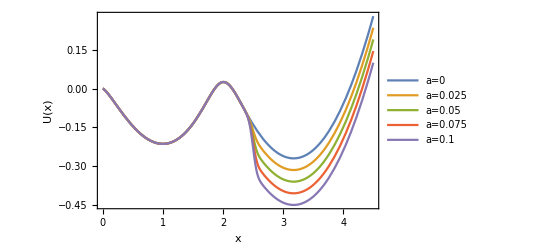

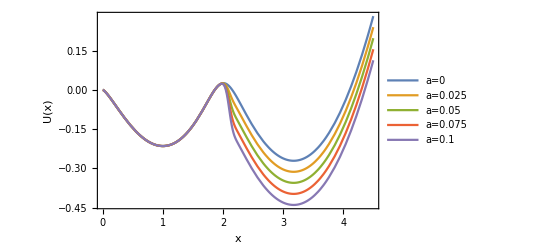

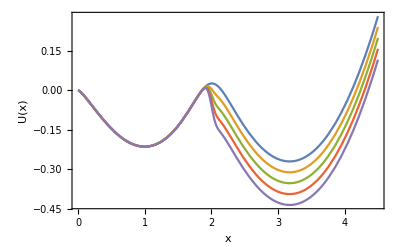

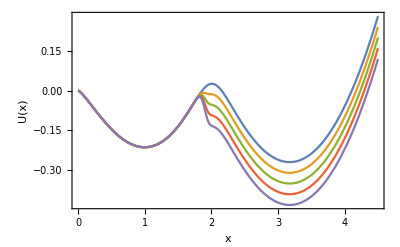

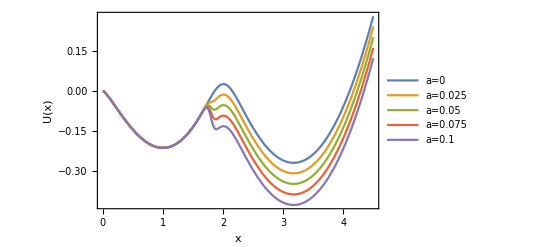

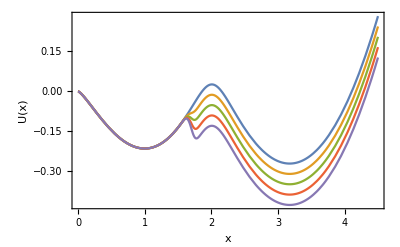

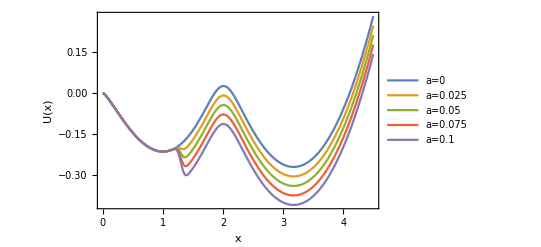

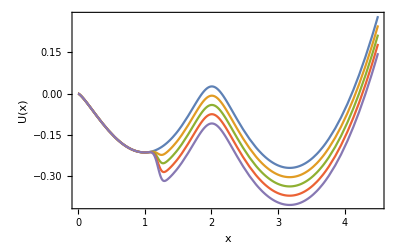

```mathematica
ClearAll[f,s,Depreciation,U,int,int2,sol,τ];

A=10;α1=0.4;s1=0.1;s2=0.2;s3=10;s5=200;d1=2;δP=0.5;n=0.5;

f[x_]:=A x^α1;
s[x_,s4_,d2_]:=s1+(s2-s1)/(1+Exp[-s3 (x-d1)])+s4 Exp[-s5 (x-d2)^2]; 
Depreciation[x_]:=(δP+n) x

(* changing s4 *)
s4Values=Range[0,0.1,0.025];
s4Values2=Range[0,0.1,0.05];

intd2is25:=NDSolveValue[{U'[x]==-(f[x]s[x,s4,2.5] -Depreciation[x]),U[0]==0},U,{x,0,4.5}];
Plot[Evaluate@Table[intd2is25[x],{s4,s4Values}],{x,0,4.5},Frame->True,FrameLabel->{"x","U(x)"},Axes->False,LabelStyle->Medium,PlotLegends->Placed[LineLegend[{"a=0","a=0.025" ,"a=0.05","a=0.075","a=0.1"},LegendLayout->{"Row",2}],{Left,Top}]]

intd2is21:=NDSolveValue[{U'[x]==-(f[x]s[x,s4,2.1] -Depreciation[x]),U[0]==0},U,{x,0,4.5}];
Plot[Evaluate@Table[intd2is21[x],{s4,s4Values}],{x,0,4.5},Frame->True,FrameLabel->{"x","U(x)"},Axes->False,LabelStyle->Medium,PlotLegends->Placed[LineLegend[{"a=0","a=0.025" ,"a=0.05","a=0.075","a=0.1"},LegendLayout->{"Row",2}],{Left,Top}]]

intd2is2:=NDSolveValue[{U'[x]==-(f[x]s[x,s4,2] -Depreciation[x]),U[0]==0},U,{x,0,4.5}];
Plot[Evaluate@Table[intd2is2[x],{s4,s4Values}],{x,0,4.5},Frame->True,FrameLabel->{"x","U(x)"},Axes->False]

intd2is19:=NDSolveValue[{U'[x]==-(f[x]s[x,s4,1.9] -Depreciation[x]),U[0]==0},U,{x,0,4.5}];
Plot[Evaluate@Table[intd2is19[x],{s4,s4Values}],{x,0,4.5},Frame->True,FrameLabel->{"x","U(x)"},Axes->False]

intd2is18:=NDSolveValue[{U'[x]==-(f[x]s[x,s4,1.8] -Depreciation[x]),U[0]==0},U,{x,0,4.5}];
Plot[Evaluate@Table[intd2is18[x],{s4,s4Values}],{x,0,4.5},Frame->True,FrameLabel->{"x","U(x)"},Axes->False,LabelStyle->Medium,PlotLegends->Placed[LineLegend[{"a=0","a=0.025" ,"a=0.05","a=0.075","a=0.1"},LegendLayout->{"Row",2}],{Left,Top}]]

intd2is17:=NDSolveValue[{U'[x]==-(f[x]s[x,s4,1.7] -Depreciation[x]),U[0]==0},U,{x,0,4.5}];
Plot[Evaluate@Table[intd2is17[x],{s4,s4Values}],{x,0,4.5},Frame->True,FrameLabel->{"x","U(x)"},Axes->False]

intd2is13:=NDSolveValue[{U'[x]==-(f[x]s[x,s4,1.3] -Depreciation[x]),U[0]==0},U,{x,0,4.5}];
Plot[Evaluate@Table[intd2is13[x],{s4,s4Values}],{x,0,4.5},Frame->True,FrameLabel->{"x","U(x)"},Axes->False,LabelStyle->Medium,PlotLegends->Placed[LineLegend[{"a=0","a=0.025" ,"a=0.05","a=0.075","a=0.1"},LegendLayout->{"Row",2}],{Left,Top}]]

intd2is12:=NDSolveValue[{U'[x]==-(f[x]s[x,s4,1.2] -Depreciation[x]),U[0]==0},U,{x,0,4.5}];
Plot[Evaluate@Table[intd2is12[x],{s4,s4Values}],{x,0,4.5},Frame->True,FrameLabel->{"x","U(x)"},Axes->False]

intd2is1:=NDSolveValue[{U'[x]==-(f[x]s[x,s4,1] -Depreciation[x]),U[0]==0},U,{x,0,4.5}];
Plot[Evaluate@Table[intd2is1[x],{s4,s4Values}],{x,0,4.5},Frame->True,FrameLabel->{"x","U(x)"},Axes->False]

(* changing d2 *)
d2Values={1,1.5,2,2.3};
ints4is05:=NDSolveValue[{U'[x]==-(f[x]s[x,0.05,d2] -Depreciation[x]),U[0]==0},U,{x,0,4.5}];
Plot[Evaluate@Table[ints4is05[x],{d2,d2Values}],{x,0,4.5},Frame->True,FrameLabel->{"x","U(x)"},Axes->False]
```

{0.,-0.025,-0.05,-0.075,-0.1}

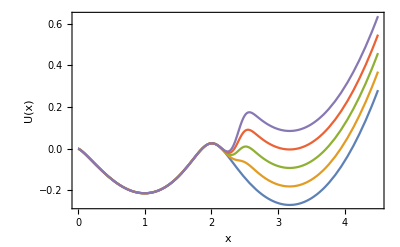

```mathematica
ClearAll[f,s,Depreciation,U,int,int2,sol,τ];

A=10;α1=0.4;s1=0.1;s2=0.2;s3=10;s5=50;d1=2;δP=0.5;n=0.5;

f[x_]:=A x^α1;
s[x_,s4_,d2_]:=s1+(s2-s1)/(1+Exp[-s3 (x-d1)])+s4 Exp[-s5 (x-d2)^2]; 
Depreciation[x_]:=(δP+n) x

(* min1=#&@@FindRoot[f[x]s[x]==Depreciation[x],{x,1}]
min2=#&@@FindRoot[f[x]s[x]==Depreciation[x],{x,2}]
min3=#&@@FindRoot[f[x]s[x]==Depreciation[x],{x,3}] *)

(* Plot[{s[x],s4 Exp[-s5 (x-d2)^2]},{x,0,4.5}]

Plot[{f[x] s[x],Depreciation[x]},{x,0,4},Frame->True, FrameLabel->{"x", "Savings (blue) and
 depreciation (orange)"}] *)

s4Values=Range[0,-0.1,-0.025]

intd2is24:=NDSolveValue[{U'[x]==-(f[x]s[x,s4,2.4] -Depreciation[x]),U[0]==0},U,{x,0,4.5}];
Plot[Evaluate@Table[intd2is24[x],{s4,s4Values}],{x,0,4.5},Frame->True,FrameLabel->{"x","U(x)"},Axes->False]
```

## Heatmap

### Changing δ (peak downwards)

Targeted group that has very low depreciation

```mathematica
ClearAll[τ,sol,int]

A=10;α1=0.4;s1=0.1;s2=0.2;s3=10;d=2;n=0.5;δ2=200;

f[x_]:=A x^α1;
s[x_]:=s1+(s2-s1)/(1+Exp[-s3 (x-d)]); 
δP[x_,δ1_,δ3_]:=0.5-δ1 Exp[-δ2 (x-δ3)^2];
Depreciation[x_,δ1_,δ3_]:=(δP[x,δ1,δ3]+n) x;

δ1Stepsize=0.1;
δ3Stepsize=0.1;

τ[x_,δ1_,δ3_]:=Module[{int,sol,τ},int=NDSolveValue[{U'[x]==-(f[x]s[x] -Depreciation[x,δ1,δ3]),U[0]==0},U,{x,0,4.5}];
sol=FindRoot[τ==NIntegrate[Exp[int[x]] NIntegrate[Exp[-int[y]],{y,1.00008,x}],{x,1.00008,3.17478}] ,{τ,1}];
τ/.sol]

yticks=MapIndexed[{#2[[1]],#}&,Range[0,0.5,δ1Stepsize]];
xticks=MapIndexed[{#2[[1]],#}&,Range[1.4,2.4,δ3Stepsize]];

data=Table[τ[x,δ1,δ3],{δ1,0,0.5,δ1Stepsize},{δ3,1.4,2.4,δ3Stepsize}]
dataRounded=Round[data,0.01]
ArrayPlot[dataRounded,Frame->True,FrameLabel->{{"δ3",None},{"δ1",None}},FrameTicks->{{yticks,None},{xticks,None}},ColorFunction->"BlueGreenYellow",PlotLegends->Automatic,Epilog->{Red,MapIndexed[Text[#1,Reverse[#2-1/2]]&,Reverse[dataRounded],{2}]}]
```

### Changing δ (peak upwards)

Targeted group that has very high depreciation

```mathematica
ClearAll[τ,sol,int]

A=10;α1=0.4;s1=0.1;s2=0.2;s3=10;d=2;n=0.5;δ2=200;

f[x_]:=A x^α1;
s[x_]:=s1+(s2-s1)/(1+Exp[-s3 (x-d)]); 
δP[x_,δ1_,δ3_]:=0.5-δ1 Exp[-δ2 (x-δ3)^2];
Depreciation[x_,δ1_,δ3_]:=(δP[x,δ1,δ3]+n) x;

δ1Stepsize=-0.1;
δ3Stepsize=0.1;

τ[x_,δ1_,δ3_]:=Module[{int,sol,τ},int=NDSolveValue[{U'[x]==-(f[x]s[x] -Depreciation[x,δ1,δ3]),U[0]==0},U,{x,0,4.5}];
sol=FindRoot[τ==NIntegrate[Exp[int[x]] NIntegrate[Exp[-int[y]],{y,1.00008,x}],{x,1.00008,3.17478}] ,{τ,1}];
τ/.sol]

yticks=MapIndexed[{#2[[1]],#}&,Range[0,-0.5,δ1Stepsize]];
xticks=MapIndexed[{#2[[1]],#}&,Range[2.2,2.6,δ3Stepsize]];

data=Table[τ[x,δ1,δ3],{δ1,0,-0.5,δ1Stepsize},{δ3,2.2,2.6,δ3Stepsize}]
dataRounded=Round[data,0.01]
ArrayPlot[dataRounded,Frame->True,FrameLabel->{{"δ3",None},{"δ1",None}},FrameTicks->{{yticks,None},{xticks,None}},ColorFunction->"BlueGreenYellow",PlotLegends->Automatic,Epilog->{Red,MapIndexed[Text[#1,Reverse[#2-1/2]]&,Reverse[dataRounded],{2}]}]
```

### Changing savings rate (peak upwards)

Selected small group gets very high savings

```mathematica
ClearAll[τ,sol,int]

A=10;α1=0.4;s1=0.1;s2=0.2;s3=10;s5=200;d1=2;δP=0.5;n=0.5;

f[x_]:=A x^α1;
s[x_,s4_,d2_]:=s1+(s2-s1)/(1+Exp[-s3 (x-d1)])+s4 Exp[-s5 (x-d2)^2]; 
Depreciation[x_]:=(δP+n) x

s4Stepsize=0.025;
d2Stepsize=0.1;

τ[x_,s4_,d2_]:=Module[{sol,τ},int=NDSolveValue[{U'[x]==-(f[x]s[x,s4,d2] -Depreciation[x]),U[0]==0},U,{x,0,4.5}];
sol=FindRoot[τ==NIntegrate[Exp[int[x]] NIntegrate[Exp[-int[y]],{y,1.00008,x}],{x,1.00008,3.17478}] ,{τ,1}];Print[sol];
τ/.sol]

yticks=MapIndexed[{#2[[1]],#}&,Range[0,0.1,s4Stepsize]];
xticks=MapIndexed[{#2[[1]],#}&,Range[1.2,2.8,d2Stepsize]];

data=ParallelTable[τ[x,s4,d2],{s4,0,0.1,s4Stepsize},{d2,1.2,2.8,d2Stepsize}]
dataRounded=Round[data,0.01]
ArrayPlot[dataRounded,Frame->True,FrameLabel->{{"d2",None},{"s4",None}},FrameTicks->{{yticks,None},{xticks,None}},ColorFunction->"BlueGreenYellow",PlotLegends->Automatic,Epilog->{Red,MapIndexed[Text[#1,Reverse[#2-1/2]]&,Reverse[dataRounded],{2}]},ImageSize->Large]
```

NIntegrate::nlim: y = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::nlim: y = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{{2.31553,2.31553,2.31553,2.31553,2.31553,2.31553,2.31553,2.31553,2.31553,2.31553,2.31553,2.31553,2.31553,2.31553,2.31553,2.31553,2.31553},{2.30124,2.29456,2.2884,2.28289,2.27817,2.27436,2.27156,2.26981,2.26907,2.26921,2.27007,2.27154,2.2736,2.27628,2.27963,2.28372,2.28863},{2.28735,2.27424,2.26215,2.25136,2.24211,2.23467,2.2292,2.22581,2.2244,2.22471,2.22642,2.22933,2.23339,2.23865,2.24523,2.25325,2.26285},{2.27385,2.25455,2.23675,2.22088,2.20731,2.1964,2.18841,2.18347,2.18145,2.18195,2.18451,2.18882,2.19482,2.20258,2.21226,2.22405,2.23816},{2.26074,2.23545,2.21217,2.19143,2.17373,2.15951,2.14912,2.14272,2.14014,2.14086,2.14426,2.14995,2.15783,2.16801,2.18067,2.19608,2.2145}}

{{2.32,2.32,2.32,2.32,2.32,2.32,2.32,2.32,2.32,2.32,2.32,2.32,2.32,2.32,2.32,2.32,2.32},{2.3,2.29,2.29,2.28,2.28,2.27,2.27,2.27,2.27,2.27,2.27,2.27,2.27,2.28,2.28,2.28,2.29},{2.29,2.27,2.26,2.25,2.24,2.23,2.23,2.23,2.22,2.22,2.23,2.23,2.23,2.24,2.25,2.25,2.26},{2.27,2.25,2.24,2.22,2.21,2.2,2.19,2.18,2.18,2.18,2.18,2.19,2.19,2.2,2.21,2.22,2.24},{2.26,2.24,2.21,2.19,2.17,2.16,2.15,2.14,2.14,2.14,2.14,2.15,2.16,2.17,2.18,2.2,2.21}}

-Graphics-

### Changing savings rate (peak downwards)

Selected small group gets very low savings (high taxes)

```mathematica
ClearAll[τ,sol,int]

A=10;α1=0.4;s1=0.1;s2=0.2;s3=10;s5=200;d1=2;δP=0.5;n=0.5;

f[x_]:=A x^α1;
s[x_,s4_,d2_]:=s1+(s2-s1)/(1+Exp[-s3 (x-d1)])+s4 Exp[-s5 (x-d2)^2]; 
Depreciation[x_]:=(δP+n) x

s4Stepsize=-0.025;
d2Stepsize=0.1;

τ[x_,s4_,d2_]:=Module[{sol,τ},int=NDSolveValue[{U'[x]==-(f[x]s[x,s4,d2] -Depreciation[x]),U[0]==0},U,{x,0,4.5}];
sol=FindRoot[τ==NIntegrate[Exp[int[x]] NIntegrate[Exp[-int[y]],{y,1.00008,x}],{x,1.00008,3.17478}] ,{τ,1}];Print[sol];
τ/.sol]

yticks=MapIndexed[{#2[[1]],#}&,Range[0,-0.1,s4Stepsize]];
xticks=MapIndexed[{#2[[1]],#}&,Range[2.2,2.8,d2Stepsize]];

data=ParallelTable[τ[x,s4,d2],{s4,0,-0.1,s4Stepsize},{d2,2.2,2.8,d2Stepsize}]
dataRounded=Round[data,-0.01]
ArrayPlot[dataRounded,Frame->True,FrameLabel->{{"d2",None},{"s4",None}},FrameTicks->{{yticks,None},{xticks,None}},ColorFunction->"BlueGreenYellow",PlotLegends->Automatic,Epilog->{Red,MapIndexed[Text[#1,Reverse[#2-1/2]]&,Reverse[dataRounded],{2}]},ImageSize->Large]
```

NIntegrate::nlim: y = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::nlim: y = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{{2.31553,2.31553,2.31553,2.31553,2.31553,2.31553,2.31553},{2.36287,2.36137,2.35925,2.35648,2.353,2.34874,2.34361},{2.41218,2.40915,2.40484,2.3992,2.39211,2.38341,2.37293},{2.46354,2.45894,2.45239,2.44378,2.43293,2.41961,2.40355},{2.51704,2.51084,2.50197,2.4903,2.47555,2.45741,2.43551}}

{{2.32,2.32,2.32,2.32,2.32,2.32,2.32},{2.36,2.36,2.36,2.36,2.35,2.35,2.34},{2.41,2.41,2.4,2.4,2.39,2.38,2.37},{2.46,2.46,2.45,2.44,2.43,2.42,2.4},{2.52,2.51,2.5,2.49,2.48,2.46,2.44}}

-Graphics-